```mathematica
coef=RandomReal[{-1, 1}, {50}];
```

```mathematica
poly[coef_][x_]:=Dot[coef, Prepend[Table[(x^n)/(n!), {n,1Length[coef]-1}], 1]]
Plot[poly[coef][x], {x, -1,1}]
```

-Graphics-

```mathematica
progressMap[func_,l_List, message_:"Complete"]:=Module[{progress=PrintTemporary["0% "<>message]}, Table[NotebookDelete[progress];progress=PrintTemporary[ToString[Round[100*i/Length[l]]]<>"% "<>message]; func[l[[i]]],{i, Length[l]}]]
```

```mathematica
GradientDescent[loss_, initialValue_List, n_:100, temp_:.05, d_:.01]:=Module[{val=initialValue}, Table[val-=temp((loss[val+#]&/@(d IdentityMatrix[Length[val]]))-loss[val])/d;, {i, n}]; val]
GridGradientDescent[loss_, ranges_, n_:100, temp_:.05, d_:.01]:=
#[[First[PositionSmallest[loss/@#]]]]&[progressMap[GradientDescent[loss, #, n, temp,d]&,Flatten[Table@@Prepend[ranges, ranges[[All, 1]]], Length[ranges]-1], "Of Descents Calculated"]]
```

```mathematica
f[x_]:=Cos[2Pi x]
```

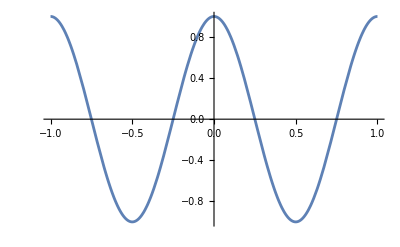

```mathematica
Plot[f[x], {x, -1, 1}]
```

```mathematica
error[func_]:=NIntegrate[(f[w]-func[w])^2, {w, -1,1}]
```

```mathematica
eFunc[coef_]:=error[poly[coef][poly[coef][#]]&]
```

```mathematica
sol={};
ranges={};
```

```mathematica
AppendTo[sol, 0];
ranges=Table[{ranges[[i,1]], sol[[i]]-ranges[[i, 4]], sol[[i]]+ranges[[i, 4]], ranges[[i, 4]]*0.5}, {i, Length[ranges]}] ;
AppendTo[ranges, {x[Length[ranges]], -2, 2, 1}]
```

{{x[0],-0.50501,0.49499,0.25},{x[1],-1.00263,0.997367,0.5},{x[2],-2,2,1}}

```mathematica
sol=GridGradientDescent[eFunc, ranges,50]
```

$Aborted

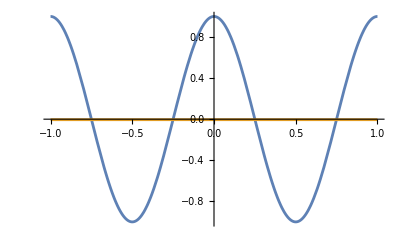

```mathematica
solf[x_]:=poly[sol][poly[sol][x]]
Plot[{f[x],solf[x]}, {x, -1,1}]
```

```mathematica
Plot3D[eFunc[{x, y}], {x, -3, 3}, {y, -3, 3}, AxesLabel->{"x", "y", "z"}]
```

-Graphics3D-

```mathematica
n=2;
s=NMinimize[eFunc[Table[x[i], {i, n}]], Table[x[i], {i, n}], Method->"NelderMead"]
```

NIntegrate::inumr: The integrand (Cos[2 π w]-x[1]-x[2] (x[1]+w x[2]))^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (Cos[2 π w]-x[1]-x[2] (x[1]+w x[2]))^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1}}.

NIntegrate::inumr: The integrand (-v1$550-v2$551 (v1$550+v2$551 w)+Cos[2 π w])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1}}.

{1.,{x[1]→-1.27916×10^-9,x[2]→0.000144871}}

```mathematica
solHist={};
pHist={};
```

```mathematica
sol=Values[Last[s]]
solf[x_]:=poly[sol][poly[sol][z]]
Plot[{f[x],solf[x]}, {x, -1,1}]
j[n_]:=(
s=NMinimize[eFunc[Table[z[i], {i, n}]], Table[z[i], {i, n}], Method->"NelderMead"];
sol=Values[Last[s]];
AppendTo[solHist, sol];
solf[x_]:=poly[sol][poly[sol][x]];
Last[AppendTo[pHist,Labeled[Plot[{Cos[2 Pi x],solf[x]}, {x, -1,1}], n]]]
)
```

{-1.27916×10^-9,0.000144871}

-Graphics-

```mathematica
j/@Range[10]
```

NIntegrate::inumr: The integrand (Cos[2 π w]-z[1])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (Cos[2 π w]-z[1])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand (-v1$588+Cos[2 π w])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand (Cos[2 π w]-z[1]-z[2] (z[1]+w z[2]))^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1}}.

NIntegrate::inumr: The integrand (-v1$591-v2$592 (v1$591+v2$592 w)+Cos[2 π w])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1}}.

NIntegrate::inumr: The integrand (Cos[2 π w]-z[1]-z[2] (z[1]+w z[2]+1/2 w^2 z[3])-1/2 z[3] (z[1]+w z[2]+1/2 w^2 z[3])^2)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1}}.

NIntegrate::inumr: The integrand (-v1$595-v2$596 (v1$595+v2$596 w+(v3$597 w^2)/2)-1/2 v3$597 (v1$595+v2$596 w+(v3$597 w^2)/2)^2+Cos[2 π w])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1}}.

NIntegrate::inumr: The integrand (Cos[2 π w]-z[1]-z[2] (z[1]+w z[2]+1/2 w^2 z[3]+1/6 w^3 z[4])-1/2 z[3] (z[1]+w z[2]+1/2 w^2 z[3]+1/6 w^3 z[4])^2-1/6 z[4] (z[1]+w z[2]+1/2 w^2 z[3]+1/6 w^3 z[4])^3)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1}}.

NIntegrate::inumr: The integrand (-v1$600-v2$601 (v1$600+v2$601 w+(v3$602 w^2)/2+(v4$603 w^3)/6)-1/2 v3$602 (v1$600+v2$601 w+(v3$602 w^2)/2+(v4$603 w^3)/6)^2-1/6 v4$603 (v1$600+v2$601 w+(v3$602 w^2)/2+(v4$603 w^3)/6)^3+Cos[2 π w])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1}}.

NIntegrate::inumr: The integrand (Cos[2 π w]-z[1]-z[2] (z[1]+w z[2]+1/2 w^2 z[3]+1/6 w^3 z[4]+1/24 w^4 z[5])-1/2 z[3] (z[1]+w z[2]+«1»+«1»+1/24 w^4 z[5])^2-1/6 z[4] (z[1]+w z[2]+1/2 w^2 z[3]+1/6 w^3 z[4]+1/24 w^4 z[5])^3-1/24 z[5] (z[1]+w z[2]+1/2 w^2 z[3]+1/6 w^3 z[4]+1/24 w^4 z[5])^4)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1}}.

NIntegrate::inumr: The integrand (-v1$606-v2$607 (v1$606+v2$607 w+(v3$608 w^2)/2+(v4$609 w^3)/6+(v5$610 w^4)/24)-1/2 v3$608 (v1$606+v2$607 w+(«1»)/2+(v4$609 «1»)/6+(v5$610 w^4)/24)^2-1/6 v4$609 (v1$606+«3»+(«6»«1»«1»)/24)^3-1/24 v5$610 (v1$606+v2$607 w+(v3$608 w^2)/2+(v4$609 w^3)/6+(v5$610 w^4)/24)^4+Cos[2 π w])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1}}.

NIntegrate::inumr: The integrand (Cos[2 π w]-z[1]-z[2] (z[1]+w z[2]+1/2 w^2 z[3]+1/6 w^3 z[4]+1/24 w^4 z[5]+1/120 w^5 z[6])-1/2 z[3] («1»)^2-1/6 z[4] (z[1]+«4»+«1»)^3-1/24 z[5] (z[1]+w z[2]+1/2 w^2 z[3]+1/6 w^3 z[4]+1/24 w^4 z[5]+1/120 w^5 z[6])^4-1/120 z[6] (z[1]+w z[2]+1/2 w^2 z[3]+1/6 w^3 z[4]+1/24 w^4 z[5]+1/120 w^5 z[6])^5)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1}}.

NIntegrate::inumr: The integrand (-v1$613-v2$614 (v1$613+v2$614 w+(v3$615 w^2)/2+(v4$616 w^3)/6+(v5$617 w^4)/24+(v6$618 w^5)/120)-1/2 v3$615 (v1$613+v2$614 w+«2»+(«1»)/24+(v6$618 «1»)/120)^2-1/6 v4$616 («1»)^3-1/24 v5$617 (v1$613+«5»)^4-1/120 v6$618 (v1$613+v2$614 w+(v3$615 w^2)/2+(v4$616 «1»)/6+(v5$617 w^4)/24+(v6$618 w^5)/120)^5+Cos[2 π w])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1}}.

NIntegrate::inumr: The integrand (Cos[2 π w]-z[1]-z[2] (z[1]+w z[2]+1/2 w^2 z[3]+«1»+1/24 w^4 z[5]+1/120 w^5 z[6]+1/720 w^6 z[7])-«1»-«1»-«1»-1/120 z[6] (z[1]+w z[2]+1/2 w^2 z[3]+1/6 w^3 z[4]+1/24 w^4 z[5]+1/120 w^5 z[6]+1/720 w^6 z[7])^5-1/720 z[7] (z[1]+w z[2]+1/2 w^2 z[3]+1/6 w^3 z[4]+1/24 w^4 z[5]+1/120 w^5 z[6]+1/720 w^6 z[7])^6)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1}}.

NIntegrate::inumr: The integrand (-v1$621-v2$622 (v1$621+v2$622 w+(v3$623 w^2)/2+(v4$624 w^3)/6+(v5$625 w^4)/24+(v6$626 w^5)/120+(v7$627 w^6)/720)-1/2 v3$623 (v1$621+«5»+(«6» «1»)/720)^2-1/6 v4$624 («1»)^3-«1»-1/120 v6$626 («1»)^5-1/720 v7$627 (v1$621+v2$622 w+(v3$623 «1»)/2+(«1»)/6+(«6»«1»«1»)/24+(v6$626 w^5)/120+(v7$627 w^6)/720)^6+Cos[2 π w])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1}}.

$Aborted

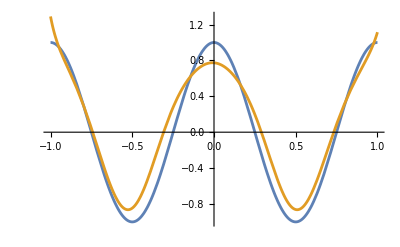
-Graphics-7

```mathematica
Last[pHist]
```